# Free energy relationships for nonadiabatic ET, PT, and PCET

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

### Accuracy settings

```mathematica
AccN=50;
```

## Marcus ET free energy curves

```mathematica
GR[x_,λ_]:=1/(4λ)(x+λ)^2;
GP[x_,λ_]:=1/(4λ)(x-λ)^2;
```

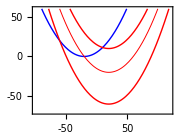

```mathematica
Plot[{GR[x,20],GP[x,20]+10,GP[x,20]-20,GP[x,20]-60},{x,-100,120},FrameTicks->{{{-50,0,50},None},{{-50,0,50},None}},PlotRange->{-70,60},Axes->False,Frame->True,PlotStyle->{{Blue,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[0.7]},{Red,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[0.75],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},ImageSize->Small,AspectRatio->0.75,GridLines->{None,None},FrameLabel->{"Solvent coordinate (kcal/mol)","Free Energy (kcal/mol)"}]
```

## Model parameters

Electronic coupling (kcal/mol):

```mathematica
V=0.03`50*ev2kcal
```

0.6918186562200262390991977597542197542932531705578

Frequencies of the quantum mode for the reactant and product proton potentials (cm^-1):

```mathematica
f1=3000.0`50;
f2=3000.0`50;
```

Minima of the reactant and product potentials (Å→ Bohr):

```mathematica
xm1=0;
xm2=0.5`50*a2bohr;
```

Harmonic potentials (kcal/mol):

```mathematica
U1[x_,m_,f_]:=au2kcal 1/2 m*Dalton*(f*cm2au)^2(x-xm1)^2;
U2[x_,m_,f_]:=au2kcal 1/2 m*Dalton*(f*cm2au)^2(x-xm2)^2;
```

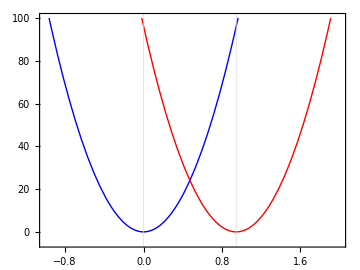

```mathematica
Plot[{U1[x,MassH,f1],U2[x,MassH,f2]},{x,-1.0,2.0},Axes->False,Frame->True,PlotStyle->{{Blue,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]}},PlotRange->{-5,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{xm1,xm2},None},AspectRatio->0.75]
```

Temperature (K):

```mathematica
T=300;
β=1/(kb*T);
```

## Harmonic oscillator energies and wavefunction overlaps

Harmonic energy levels (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*omega*(n+1/2)];
```

Harmonic wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

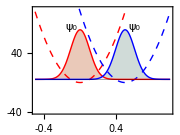

```mathematica
GraphS00=Plot[{U1[x a2bohr,MassH,f1],U2[x a2bohr,MassH,f2]-HarmEnergy[0,f1]+HarmEnergy[0,f1],HarmEnergy[0,f1]+40*HarmWavefunction[0,f1,x a2bohr-xm1,M->MassH],HarmEnergy[0,f2]+40*HarmWavefunction[0,f2,x a2bohr-xm2,M->MassH],HarmEnergy[0,f1]},{x,-0.5,1.0},FrameTicks->{{{-40,0,40,80},None},{{-0.4,0,0.4,0.8},None}},PlotRange->{-40,100},Axes->False,Frame->True,PlotStyle->{{Red,Dashed,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Black,AbsoluteThickness[0.25]}},FrameStyle->AbsoluteThickness[0.5],BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ImageSize->Small,AspectRatio->0.75,GridLines->{None,None},Filling->{3->{5,{LightRed}},4->{5,LightBlue},3->{4}},FrameLabel->{"Proton coordinate (Bohr)","Energy (kcal/mol)","","Wavefunction"},Epilog->{Inset[Subscript[ψ, 0],{0.6,75}],Inset[Subscript[ψ, 0],{-0.1,75}]}]
```

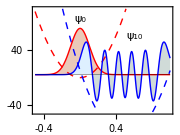

```mathematica
GraphS010=Plot[{U1[x a2bohr,MassH,f1],U2[x a2bohr,MassH,f2]-HarmEnergy[10,f1]+HarmEnergy[0,f1],HarmEnergy[0,f1]+40*HarmWavefunction[0,f1,x a2bohr-xm1,M->MassH],HarmEnergy[0,f2]+40*HarmWavefunction[10,f2,x a2bohr-xm2,M->MassH],HarmEnergy[0,f1]},{x,-0.5,1.0},FrameTicks->{{{-40,0,40,80},None},{{-0.4,0,0.4,0.8},None}},PlotRange->{-50,100},Axes->False,Frame->True,PlotStyle->{{Red,Dashed,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Black,AbsoluteThickness[0.25]}},FrameStyle->AbsoluteThickness[0.5],BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ImageSize->Small,AspectRatio->0.75,GridLines->{None,None},Filling->{3->{5,{LightRed}},4->{5,LightBlue},3->{4}},FrameLabel->{"Proton coordinate (Bohr)","Energy (kcal/mol)","","Wavefunction"},Epilog->{Inset[Subscript[ψ, 10],{0.6,60}],Inset[Subscript[ψ, 0],{0,85}]}]
```

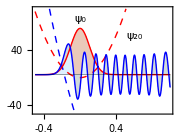

```mathematica
GraphS020=Plot[{U1[x a2bohr,MassH,f1],U2[x a2bohr,MassH,f2]-HarmEnergy[20,f1]+HarmEnergy[0,f1],HarmEnergy[0,f1]+40*HarmWavefunction[0,f1,x a2bohr-xm1,M->MassH],HarmEnergy[0,f2]+40*HarmWavefunction[20,f2,x a2bohr-xm2,M->MassH],HarmEnergy[0,f1]},{x,-0.5,1.0},FrameTicks->{{{-40,0,40,80},None},{{-0.4,0,0.4,0.8},None}},PlotRange->{-50,100},Axes->False,Frame->True,PlotStyle->{{Red,Dashed,AbsoluteThickness[1.0]},{Blue,Dashed,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Black,AbsoluteThickness[0.25]}},FrameStyle->AbsoluteThickness[0.5],BaseStyle->{FontSize->9,FontFamily->"Helvetica"},ImageSize->Small,AspectRatio->0.75,GridLines->{None,None},Filling->{3->{5,{LightRed}},4->{5,LightBlue},3->{4}},FrameLabel->{"Proton coordinate (Bohr)","Energy (kcal/mol)","","Wavefunction"},Epilog->{Inset[Subscript[ψ, 20],{0.6,60}],Inset[Subscript[ψ, 0],{0,85}]}]
```

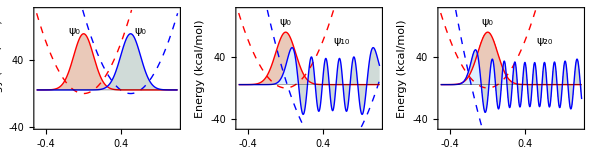

```mathematica
GraphicsGrid[{{GraphS00,GraphS010,GraphS020}}]
```

Overlap integrals (in this expression the second oscillator is d Bohr to the left of the first one):

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->100}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

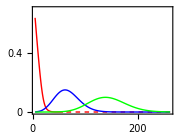

```mathematica
GraphS0nu=ListLinePlot[{Table[{HarmEnergy[i,3000],HarmOverlap[0,i,3000,3000,0.1a2bohr]^2},{i,0,30,1}],Table[{HarmEnergy[i,3000],HarmOverlap[0,i,3000,3000,0.40a2bohr]^2},{i,0,30,1}],Table[{HarmEnergy[i,3000],HarmOverlap[0,i,3000,3000,0.60a2bohr]^2},{i,0,30,1}]},PlotStyle->{Red,Blue,Green},FrameTicks->{{{0,0.2,0.4,0.6},None},{{0,100,200,300},None}},PlotRange->{0,0.7},FrameLabel->{"Vibrational energy (kcal/mol)","Franck-Condon factor"},Axes->False,Frame->True,BaseStyle->{FontSize->9,FontFamily->"Helvetica",AbsoluteThickness[1.0]},ImageSize->Small,FrameStyle->AbsoluteThickness[0.5],AspectRatio->0.75,InterpolationOrder->3,Filling->None]
```

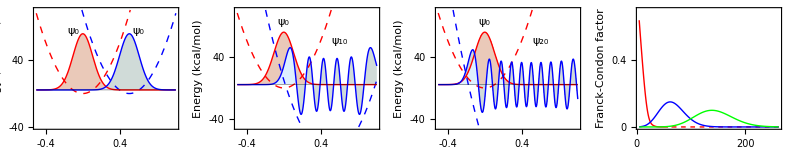

```mathematica
GraphicsGrid[{{GraphS00,GraphS010,GraphS020,GraphS0nu}}]
```

1D overlaps as a function of the vibrational quantum number <0|i>

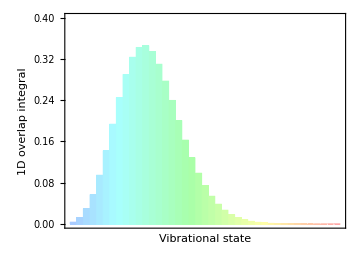

```mathematica
BarChart[
{Table[
HarmOverlap[0,i,3000,3000,0.5a2bohr],
{i,0,40,1}]},
PlotRange->{0,0.4},FrameLabel->{"Vibrational state","1D overlap integral"},Axes->False,Frame->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica",AbsoluteThickness[1.0]},ImageSize->Medium,FrameStyle->AbsoluteThickness[0.5],AspectRatio->0.75]
```

1D vibronic coupling as a function of the vibrational quantum number <0|i>

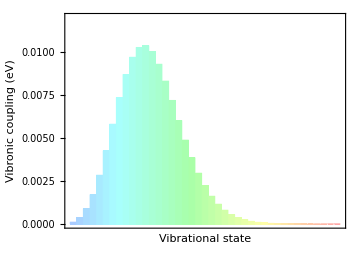

```mathematica
BarChart[
{Table[
0.03*HarmOverlap[0,i,3000,3000,0.5a2bohr],
{i,0,40,1}]},
PlotRange->{0,0.012},FrameLabel->{"Vibrational state","Vibronic coupling (eV)"},Axes->False,Frame->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica",AbsoluteThickness[1.0]},ImageSize->Medium,FrameStyle->AbsoluteThickness[0.5],AspectRatio->0.75]
```

```mathematica
couplingsTable=Table[{i,1.00*HarmOverlap[0,i,3000,3000,0.5a2bohr],
0.03*HarmOverlap[0,i,3000,3000,0.5a2bohr]},
{i,0,40,1}];
```

```mathematica
Directory[]
```

/Users/souda

```mathematica
Export["coup.dat",couplingsTable,"Table"]
```

coup.dat

Overlap of three-dimensional wavefunctions:

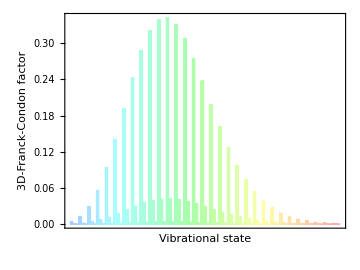

```mathematica
BarChart[
{Flatten[Table[
Abs[HarmOverlap[0,i,3000,3000,0.5a2bohr]
HarmOverlap[0,j,100,100,0.1a2bohr]],
{i,0,30,1},{j,0,2,1}]]},
PlotRange->All,FrameLabel->{"Vibrational state","3D-Franck-Condon factor"},Axes->False,Frame->True,BaseStyle->{FontSize->9,FontFamily->"Helvetica",AbsoluteThickness[1.0]},ImageSize->Medium,FrameStyle->AbsoluteThickness[0.5],AspectRatio->0.75]
```

## Partition function and Boltzmann factors

Partition function for harmonic oscillator (zero energy is at the bottom of the potential well):

```mathematica
Z[f_,T_]:=(Exp[(f*cm2au)/(2 kb T)]-Exp[-(f*cm2au)/(2kb T)])^-1;
```

Boltzmann weights:

```mathematica
P[n_,f_,T_]:=1/Z[f,T] Exp[-1/(kb T)(n+1/2)f*cm2au];
```

## General ET/PT/PCET electronically nonadiabatic rate constant (fixed donor-acceptor distance)

### Function

Rate constant (s^-1): kgen[T_,  λ_,  dG_,  f1_,  f2_,  d_,  μmax_,  νmax_]
T - temperature (K);
λ - solvent reorganization energy (kcal/mol);
dG - reaction free energy, [product - reactant] (kcal/mol);
f1, f2 - frequencies for reactant and product harmonic potentials (cm^-1);
d - distance between the potential minima (Bohr);
μmax, νmax - highest included quantum numbers for reactant and product vibrational states.

```mathematica
kgen[T_,λ_,dG_,f1_,f2_,d_,μmax_,νmax_,OptionsPattern[{M->MassH}]]:=Module[{mass,lambda,Δ,S,S2,dϵ,A},
mass=OptionValue[M];
lambda=λ*kcal2au;
Δ=dG*kcal2au;
A=10^12*ps2au*Sqrt[π/(lambda*kb*T)]*(V*kcal2au)^2;
Array[S2,{μmax+1,νmax+1},{0,0}];
Array[dϵ,{μmax+1,νmax+1},{0,0}];
Do[S=HarmOverlap[μ,ν,f1,f2,d,M->mass];S2[μ,ν]=S^2,{μ,0,μmax,1},{ν,0,νmax,1}];
Do[dϵ[μ,ν]=(HarmEnergy[ν,f2]-HarmEnergy[μ,f1])*kcal2au,{μ,0,μmax,1},{ν,0,νmax,1}];
A*Sum[P[μ,f1,T]Sum[S2[μ,ν]*Exp[-(Δ+lambda+dϵ[μ,ν])^2/(4*lambda*kb*T)],{ν,0,νmax,1}],{μ,0,μmax,1}]
];
```

### Convergence of the rate constant:

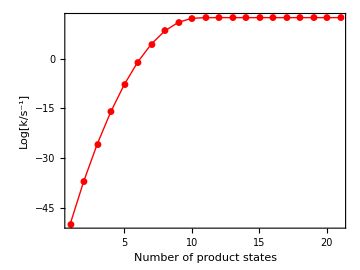

```mathematica
ListLinePlot[Table[{i+1,Log[10,kgen[300,20,-100,3000,3000,1/2 a2bohr,0,i,M->MassH]]},{i,0,20,1}],Axes->False,Frame->True,PlotMarkers->Automatic,PlotRange->All,PlotStyle->{{Red,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Number of product states","Log[k/s^-1]"},ImageSize->Medium,AspectRatio->0.75]
```

### Energy gap law:

ET (λ = 20 kcal/mol; M = 10 amu; ω_R=ω_P=500 cm^-1; ΔR = 0.1 Å):

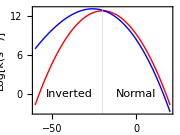

```mathematica
ListLinePlot[{
Table[{x,Log[10,kgen[300,20,x,600,600,0.1a2bohr,0,0,M->10]]},{x,-60,20,1}],
Table[{x,Log[10,kgen[300,20,x,600,600,0.2a2bohr,0,20,M->10]]},{x,-60,20,1}]},
Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},FrameLabel->{"Reaction free energy (kcal/mol)","Log[k(s^-1)]"},ImageSize->Small,AspectRatio->0.75,GridLines->{{-20},None},Epilog->{Inset["Inverted",{-40,0}],Inset["Normal",{0,0}]}]
```

electronically nonadiabatic PT/PCET:

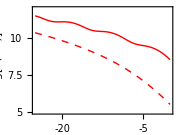

```mathematica
ListLinePlot[{
Table[{x,Log[10,kgen[300,5,x,2500,2500,0.5a2bohr,0,20]]},{x,-25,0,0.5}],Table[{x,Log[10,kgen[300,20,x,2500,2500,0.5a2bohr,0,20]]},{x,-25,0,0.5}]},
Axes->False,Frame->True,FrameTicks->{{{5,7.5,10},None},{{-20,-15,-10,-5,0},None}},PlotRange->{5,12},
PlotStyle->{
{Red,AbsoluteThickness[1.0]},
{Red,Dashed,AbsoluteThickness[1.0]},
{Blue,AbsoluteThickness[1.0]},
{Blue,Dashed,AbsoluteThickness[1.0]}
},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},FrameLabel->{"Reaction free energy (kcal/mol)","Log[k(s^-1)]"},ImageSize->Small,AspectRatio->0.75]
```

```mathematica
kgen[300,5,0,2500,2500,0.5a2bohr,0,20]
```

3.50746713264616264661170743850128828217357511565×10^8

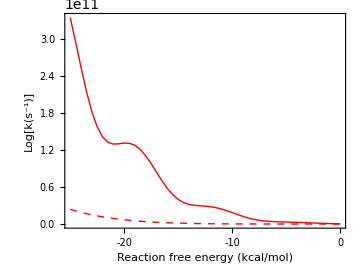

```mathematica
ListLinePlot[{
Table[{x,kgen[300,5,x,2500,2500,0.5a2bohr,0,20]},{x,-25,0,0.5}],Table[{x,kgen[300,20,x,2500,2500,0.5a2bohr,0,20]},{x,-25,0,0.5}]},
Axes->False,Frame->True,FrameTicks->{{All,None},{{-20,-10,0},None}},PlotRange->All,
PlotStyle->{
{Red,AbsoluteThickness[1.0]},
{Red,Dashed,AbsoluteThickness[1.0]},
{Blue,AbsoluteThickness[1.0]},
{Blue,Dashed,AbsoluteThickness[1.0]}
},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},FrameLabel->{"Reaction free energy (kcal/mol)","Log[k(s^-1)]"},ImageSize->Medium,AspectRatio->0.75]
```

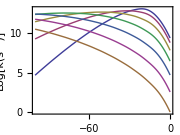

```mathematica
ListLinePlot[Table[Table[{x,Log[10,kgen[300,20,x,3000,3000,d a2bohr,0,20]]},{x,-100,0,1}],{d,0.1,0.7,0.1}],Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->AbsoluteThickness[1.0],FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},PlotRange->All,FrameLabel->{"Reaction free energy (kcal/mol)","Log[k(s^-1)]"},ImageSize->Small,AspectRatio->0.75]
```

## Two-mode nonadiabatic rate expression

### Function

Rate constant (s^-1): kgen2[T_,  λ_,  dG_,  f1_,  f2_,  d_,  μmax_,  νmax_]
T - temperature (K);
λ - solvent reorganization energy (kcal/mol);
dG - reaction free energy, [product - reactant] (kcal/mol);
f1, f2 - frequencies for reactant and product harmonic potentials (cm^-1);
d - distance between the potential minima (Bohr);
μmax, νmax - highest included quantum numbers for reactant and product vibrational states.

```mathematica
kgen2[T_,λ_,dG_,{f1r_,f1p_,d1_,μ1max_,ν1max_},{f2r_,f2p_,d2_,μ2max_,ν2max_},OptionsPattern[{M1->MassH,M2->10}]]:=Module[{mass1,mass2,lambda,Δ,S,S1SQ,S2SQ,dϵ1,dϵ2,A},
mass1=OptionValue[M1];
mass2=OptionValue[M2];
lambda=λ*kcal2au;
Δ=dG*kcal2au;
A=10^12*ps2au*Sqrt[π/(lambda*kb*T)]*(V*kcal2au)^2;
Array[S1SQ,{μ1max+1,ν1max+1},{0,0}];
Array[S2SQ,{μ2max+1,ν2max+1},{0,0}];
Array[dϵ1,{μ1max+1,ν1max+1},{0,0}];
Array[dϵ2,{μ2max+1,ν2max+1},{0,0}];
Do[
S=HarmOverlap[μ,ν,f1r,f1p,d1,M->mass1];S1SQ[μ,ν]=S^2,{μ,0,μ1max,1},
{ν,0,ν1max,1}];
Do[
S=HarmOverlap[μ,ν,f2r,f2p,d2,M->mass2];S2SQ[μ,ν]=S^2,{μ,0,μ2max,1},
{ν,0,ν2max,1}];
Do[
dϵ1[μ,ν]=(HarmEnergy[ν,f1p]-HarmEnergy[μ,f1r])*kcal2au,{μ,0,μ1max,1},
{ν,0,ν1max,1}];
Do[
dϵ2[μ,ν]=(HarmEnergy[ν,f2p]-HarmEnergy[μ,f2r])*kcal2au,{μ,0,μ2max,1},
{ν,0,ν2max,1}];
A*Sum[P[μ1,f1r,T]P[μ2,f2r,T]Sum[S1SQ[μ1,ν1]*S2SQ[μ2,ν2]*Exp[-(Δ+lambda+dϵ1[μ1,ν1]+dϵ2[μ2,ν2])^2/(4*lambda*kb*T)],{ν1,0,ν1max,1},{ν2,0,ν2max,1}],{μ1,0,μ1max,1},{μ2,0,μ2max,1}]
];
```

### Plots:

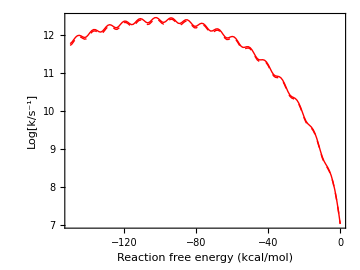

```mathematica
ListLinePlot[{Table[{x,Log[10,kgen2[300,8,x,{3000,3000,1/2 a2bohr,0,20},{600,600,1/10 a2bohr,0,20},M1->MassH,M2->MassH]]},{x,-150,0,1}],Table[{x,Log[10,kgen2[300,8,x,{3000,3000,1/2 a2bohr,0,20},{600,600,1/10 a2bohr,0,0},M1->MassH,M2->MassH]]},{x,-150,0,1}]},PlotMarkers->None,Axes->False,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Red,Dashed,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Reaction free energy (kcal/mol)","Log[k/s^-1]"},ImageSize->Medium,AspectRatio->0.75]
```

## Kiefer-Hynes expressions for nonadiabatic PT (fixed donor-acceptor distance)

### Nonadiabatic coupling for electronically adiabatic PT (semiclassical tunneling)

```mathematica
VPT[nr_,np_,fr_,fp_,ft_,vts_]:=Module[{or,op,ot,vt},
or=fr*cm2au;
op=fp*cm2au;
ot=ft*cm2au;
vt=vts*kcal2au;
If[vt-((nr+1)*or+np*op)/2<0,1/2 Sqrt[or*op],1/(2π)Sqrt[or*op]*Exp[-π/ot(vt-((nr+1)*or+np*op)/2)]]
];
```

The above expression diverges from higher vibrational states...

```mathematica
VPT[0,0,3000,3000,2500,15]au2kcal
```

0.0123204898132150120915289794146859877358393593687

```mathematica
kb 300 au2kcal
```

0.5961647729655

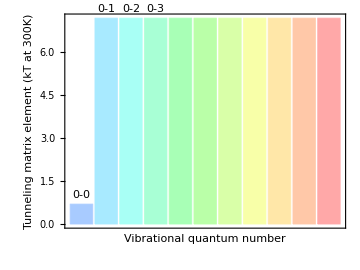

```mathematica
BarChart[{Table[VPT[0,i,3000,3000,2500,7]/(300 kb),{i,0,10,1}]},PlotRange->All,FrameLabel->{"Vibrational quantum number","Tunneling matrix element (kT at 300K)"},Frame->True,BaseStyle->{FontSize->10,FontFamily->"Helvetica"},ImageSize->Medium,FrameStyle->AbsoluteThickness[0.75],AspectRatio->0.75,FrameTicks->{None,Automatic},ChartLabels->Placed[{"0-0","0-1","0-2","0-3"},Above]]
```

```mathematica
7-1/2 f1*cm2au*au2kcal
```

2.711271365120534573021793791653457313254407919195

### Rate expression for electronically adiabatic PT (tunneling in the adiabatic potential)

```mathematica
kead[T_,λ_,dG_,fr_,fp_,ft_,ets_,μmax_,νmax_]:=
Module[{Es,dG0,dϵ,A,V00,Vmn,dϵ00},
Es=λ*kcal2au;
dG0=dG*kcal2au;
A=10^12*ps2au*Sqrt[π/(Es*kb*T)];
Array[dϵ,{μmax+1,νmax+1},{0,0}];
Array[Vmn,{μmax+1,νmax+1},{0,0}];
Do[
dϵ[μ,ν]=(HarmEnergy[ν,fp]-HarmEnergy[μ,fr])*kcal2au;
Vmn[μ,ν]=VPT[μ,ν,fr,fp,ft,ets],
{μ,0,μmax,1},{ν,0,νmax,1}
];
dϵ00=dϵ[0,0];
A*Sum[P[μ,fr,T]Sum[Vmn[μ,ν]^2*Exp[-(dG0+Es+dϵ[μ,ν]-dϵ00)^2/(4*Es*kb*T)],{ν,0,νmax,1}],{μ,0,μmax,1}]
];
```

```mathematica
kead[300,5,0,3000,3000,2500,5,0,10]
```

8.2869262854044703723641626608281812801630184603×10^12

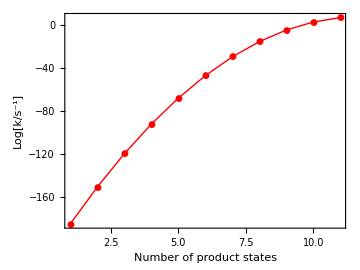

```mathematica
ListLinePlot[Table[{i+1,Log[10,kead[300,8,-100,3000,3000,2500,20,0,i,M->MassH]]},{i,0,10,1}],Axes->False,Frame->True,PlotMarkers->Automatic,PlotRange->All,PlotStyle->{{Red,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Number of product states","Log[k/s^-1]"},ImageSize->Medium,AspectRatio->0.75]
```

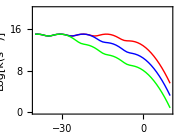

```mathematica
ListLinePlot[{
Table[{x,Log[10,kead[300,5,x,3000,3000,2000,5,0,20]]},{x,-40,10,1}],
Table[{x,Log[10,kead[300,5,x,3000,3000,2000,10,0,20]]},{x,-40,10,1}],
Table[{x,Log[10,kead[300,5,x,3000,3000,2000,15,0,20]]},{x,-40,10,1}]},
PlotRange->{0,20},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Green,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->10,FontFamily->"Helvetica"},FrameLabel->{"Reaction free energy (kcal/mol)","Log[k(s^-1)]"},ImageSize->Small,AspectRatio->0.75]
```

## Figures 4a and 4b

### PCET: Energy gap law when the donor-acceptor distance changes along with the reaction free energy

```mathematica
Array[x,40];
Array[d,40];
```

```mathematica
For[i=40,i>0,i--,x[i]=0-(i-1)*1;d[i]=0.5*a2bohr+(i-1)*a2bohr/140];
```

```mathematica
Table[x[i],{i,1,40}]
```

{0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20,-21,-22,-23,-24,-25,-26,-27,-28,-29,-30,-31,-32,-33,-34,-35,-36,-37,-38,-39}

```mathematica
Table[bohr2a*d[i]+2.0,{i,1,40}]
```

{2.5,2.50714,2.51429,2.52143,2.52857,2.53571,2.54286,2.55,2.55714,2.56429,2.57143,2.57857,2.58571,2.59286,2.6,2.60714,2.61429,2.62143,2.62857,2.63571,2.64286,2.65,2.65714,2.66429,2.67143,2.67857,2.68571,2.69286,2.7,2.70714,2.71429,2.72143,2.72857,2.73571,2.74286,2.75,2.75714,2.76429,2.77143,2.77857}

Slope:

```mathematica
((d[40]-d[1])bohr2a)/(x[40]-x[1])
```

-0.00714286

```mathematica
kgen0=kgen[300,20,0,3000,3000,d[1],1,20]
```

50427.946335652221101459190578461010990269171774

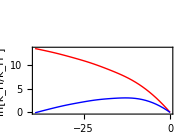

```mathematica
pcetcombined=ListLinePlot[
{Table[{x[i],Log[kgen[300,20,x[i],3000,3000,d[1],1,20]/kgen0]},{i,1,40}],
Table[{x[i],Log[kgen[300,20,x[i],3000,3000,d[i],1,20]/kgen0]},{i,1,40}]},
Axes->False,Frame->True,FrameTicks->{{All,None},{All,None}},PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->9,FontFamily->"Helvetica"},FrameLabel->{"ΔG^0 (kcal/mol)","ln[k_H/k_H^0]"},ImageSize->Small,AspectRatio->0.75,Epilog->{Inset["(b)",{-4,23}]}]
```

### electronically adiabatic PT: Energy gap law when the proton barrier height changes along with the reaction free energy

```mathematica
Array[xa,60];
Array[eb,60];
```

```mathematica
For[i=60,i>0,i--,xa[i]=5-(i-1)*0.5;eb[i]=7+(i-1)/2.5];
```

```mathematica
Table[xa[i],{i,1,60}]
```

{5,4.5,4.,3.5,3.,2.5,2.,1.5,1.,0.5,0.,-0.5,-1.,-1.5,-2.,-2.5,-3.,-3.5,-4.,-4.5,-5.,-5.5,-6.,-6.5,-7.,-7.5,-8.,-8.5,-9.,-9.5,-10.,-10.5,-11.,-11.5,-12.,-12.5,-13.,-13.5,-14.,-14.5,-15.,-15.5,-16.,-16.5,-17.,-17.5,-18.,-18.5,-19.,-19.5,-20.,-20.5,-21.,-21.5,-22.,-22.5,-23.,-23.5,-24.,-24.5}

```mathematica
Table[eb[i],{i,1,60}]
```

{7,7.4,7.8,8.2,8.6,9.,9.4,9.8,10.2,10.6,11.,11.4,11.8,12.2,12.6,13.,13.4,13.8,14.2,14.6,15.,15.4,15.8,16.2,16.6,17.,17.4,17.8,18.2,18.6,19.,19.4,19.8,20.2,20.6,21.,21.4,21.8,22.2,22.6,23.,23.4,23.8,24.2,24.6,25.,25.4,25.8,26.2,26.6,27.,27.4,27.8,28.2,28.6,29.,29.4,29.8,30.2,30.6}

Slope:

```mathematica
(eb[30]-eb[1])/(xa[30]-xa[1])
```

-0.8

```mathematica
kead0=kead[300,8,0,3000,3000,2500,eb[1],1,20]
```

3.2207528893982505367824214149047806026795839449×10^11

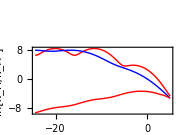

```mathematica
ptcombined=ListLinePlot[{Table[{xa[i],Log[kead[300,3,xa[i],3000,3000,2500,eb[1],1,20]/kead0]},{i,1,60}],
Table[{xa[i],Log[kead[300,8,xa[i],3000,3000,2500,eb[1],1,20]/kead0]},{i,1,60}],
Table[{xa[i],Log[kead[300,8,xa[i],3000,3000,2500,eb[i],1,20]/kead0]},{i,1,60}]},
Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[0.7],BaseStyle->{FontSize->9,FontFamily->"Helvetica"},FrameLabel->{"ΔG^0 (kcal/mol)","ln[k_H/k_H^0]"},ImageSize->Small,AspectRatio->0.75,InterpolationOrder->2,Epilog->{Inset["(a)",{3,30}]}]
```

### Figure 4

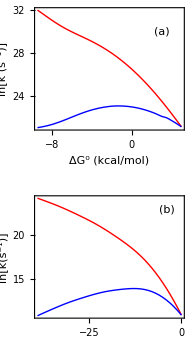

```mathematica
GraphicsGrid[{{ptcombined},{pcetcombined}},Spacings->{0,30}]
```